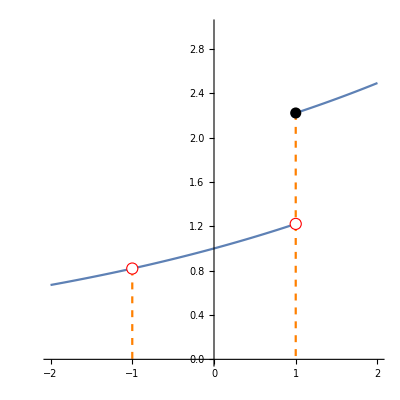

```mathematica
f1=Plot[Piecewise[{{E^(0.2x),x<1},{E^(0.2x)+1,x>1}}],{x,-2,2},Epilog->{Disk[{1,E^(0.2)+1},Offset[4]],EdgeForm[Red],White,Disk[{1,E^(0.2)},Offset[4]],Disk[{-1,E^(-0.2)},Offset[4]]},AspectRatio->1,PlotRange->{0,3}];
f2=ContourPlot[x==-1,{x,-2,2},{y,0,E^(-0.2)},ContourStyle->{Dashed,Orange}];
f3=ContourPlot[x==1,{x,-2,2},{y,0,E^(0.2)+1},ContourStyle->{Dashed,Orange}];
Show[f1,f2,f3]
```

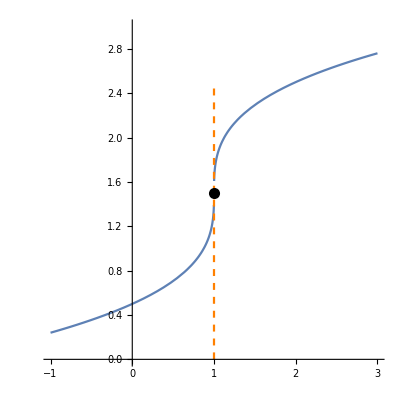

```mathematica
f11=Plot[Piecewise[{{(x-1)^(1/3)+1.5,x>=1},{-(1-x)^(1/3)+1.5,x<1}}],{x,-1,3},Epilog->{Disk[{1,1.5},Offset[4]]},PlotRange->{0,3},AspectRatio->1];
f12=ContourPlot[x==1,{x,0,2},{y,0,2.5},ContourStyle->{Dashed,Orange}];
Show[f11,f12]
```

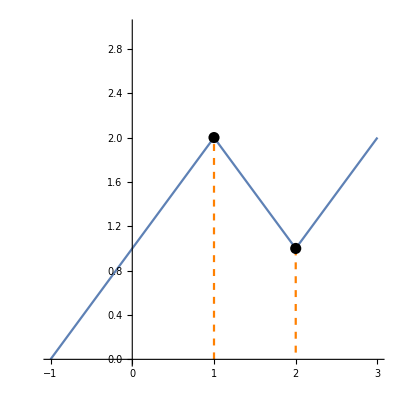

```mathematica
f21=Plot[Piecewise[{{x+1,x<1},{-x+3,1<x<2},{x-1,x>2}}],{x,-1,3},Epilog->{Disk[{1,2},Offset[4]],Disk[{2,1},Offset[4]]},PlotRange->{0,3},AspectRatio->1];
f22=ContourPlot[x==1,{x,0,2},{y,0,2},ContourStyle->{Dashed,Orange}];
f23=ContourPlot[x==2,{x,1,2.2},{y,0,1},ContourStyle->{Dashed,Orange}];
Show[f21,f22,f23]
```

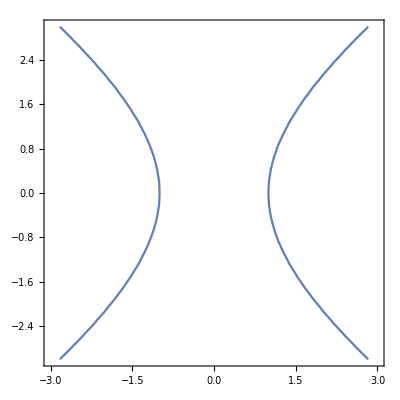

```mathematica
ContourPlot[y^2==x^2-Cos[y],{x,-3,3},{y,-3,3}]
```

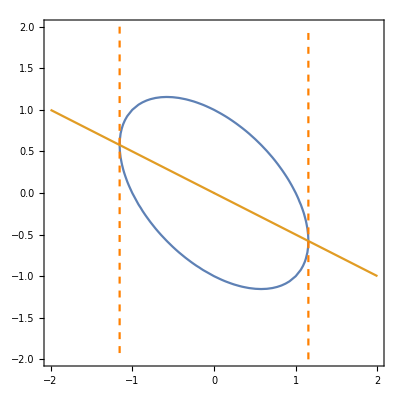

```mathematica
f21=ContourPlot[{x^2+x*y+y^2==1,x==-2y},{x,-2,2},{y,-2,2}];
f22=ContourPlot[{x==2Sqrt[3]/3,x==-2Sqrt[3]/3},{x,-2,2},{y,-2,2},ContourStyle->{{Dashed,Orange},{Dashed,Orange}}];
Show[f21,f22]
```

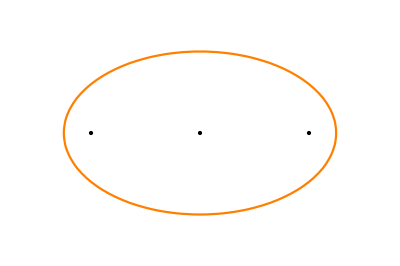

```mathematica
f31=ContourPlot[x^2/(25)+y^2/(9)==1,{x,-6,6},{y,-4,4},AspectRatio->Automatic,Frame->False,ContourStyle->Orange];
f32=Graphics[{Point[{4,0}],Point[{-4,0}],Point[{0,0}]}];
Show[f31,f32]
```

```mathematica
Plot3D[Sqrt[x^2+y^2],{x,-3,3},{y,-3,3},PlotRange->{0,2},Boxed->False]
```

-Graphics3D-

```mathematica
f41=ContourPlot3D[2z^2==x^2+y^2,{x,-3,3},{y,-3,3},{z,0,2},Boxed->False,Axes->False,ContourStyle->{Opacity[0.1],Orange},Mesh->None,PlotPoints->20];
f42=RegionPlot3D[2z^2>x^2+y^2,{x,-3,3},{y,-3,3},{z,0,1.3},Mesh->None];
Show[f41,f42,ViewPoint->{4,1,2}]
```

-Graphics3D-

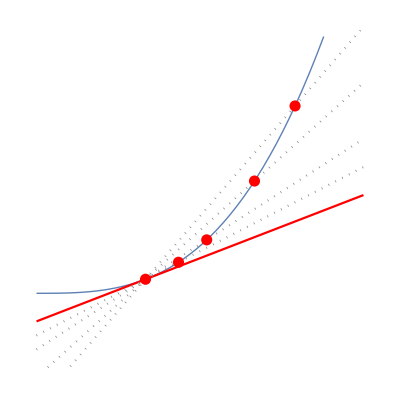

```mathematica
fx1=Function[x,x^3+5];f51=Plot[{fx1[x],3x+3},{x,0,3},
AspectRatio->1,AxesOrigin->{0,0},PlotStyle->{{Thick},{Red}},Axes->None,Epilog->{Red,Disk[{1,fx1[1]},Offset[4]],Disk[{2,fx1[2]},Offset[4]],Disk[{1/2 (-1+√17),fx1[1/2 (-1+√17)]},Offset[4]],
Disk[{1/2 (-1+√13),fx1[1/2 (-1+√13)]},Offset[4]],
Disk[{1/2 (-1+√33),fx1[1/2 (-1+√33)]},Offset[4]]
}];
f52=Plot[{4x+2,5x+1,7x-1,9x-3},{x,0,3},PlotStyle->{{Gray,Dotted},{Dotted,Gray}}];
Show[f51,f52]
```

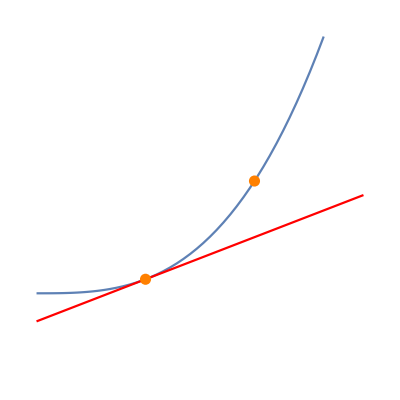

```mathematica
fx=Function[x,x^3+5];
f61=Plot[{fx[x],3x+3},{x,0,3},
AspectRatio->1,AxesOrigin->{0,0},PlotStyle->{{},{Red}},Axes->None,Epilog->{Orange,Disk[{2,fx[2]},Offset[4]],Disk[{1,fx[1]},Offset[4]]}];
Show[f61]
```

```mathematica
Solve[x^3+5==7(x-1)+6,x]
```

{{x→-3},{x→1},{x→2}}

```mathematica
256*88
```

22528

```mathematica
86*2^7
```

11008